## I. Build The Equivalent Triangulation Polygon

```mathematica
Parentheses2Polygon[s_, label_]:= Module[{chars = Characters[s], pos, rawtokens, tokens = {}, n,i, edges},
pos = Flatten[Position[chars, "A"]];
n = Length[pos] + 1;
tokens = ReadList[StringToStream[s], Word, TokenWords->{"(","A",")"}];
tokens = Select[tokens, # ≠ "A" &];
edges =Table[i<->(i+1), {i,n-1}];
(*AppendTo[edges, n<->1];*)
SplitParentheses[tokens_]:= Module[{index, k, t, t1, len = Length[tokens]},
t = Part[tokens, Range[2, len - 1]];
len = len - 2;
For[k = 1, k ≤ len - 1, k++,
	t1= Take[t, k];
	If[Length[Select[t1, # == "(" &]]==  Length[Select[t1, # == ")" &]], Return[{t1, Drop[t, k]}];];
];
Return[{{},{}}];
];

ProcessEdges[tokens_]:=Module[{e,v1, v2, t1, t2, t= SplitParentheses[tokens]},
	t1 = t[[1]];
	t2 = t[[2]];
	v1 =  ToExpression[First[Select[t[[1]], # ≠ "(" && #≠ ")"&]]];
	v2 =  ToExpression[Last[Select[t[[1]], # ≠ "(" && #≠ ")"&]]] + 1;	
	AppendTo[edges, v1<->v2];
	v1 =  ToExpression[First[Select[t[[2]], # ≠ "(" && #≠ ")"&]]];
	v2 =  ToExpression[Last[Select[t[[2]], # ≠ "(" && #≠ ")"&]]] + 1;	
	AppendTo[edges, v1<->v2];
	If[Length[t1] > 1, ProcessEdges[t1];];
	If[Length[t2] >1, ProcessEdges[t2];];
];
ProcessEdges[tokens];
circleLayout[n_]:=Table[{Cos[-2π/n i-π/2],Sin[-2π/n i-π/2]},{i,n}];
Graph[Range[n], DeleteDuplicates[edges], VertexLabels->Table[i ->label[[i]], {i, n}], VertexCoordinates-> circleLayout[n]]
]

Parentheses2Polygon[s_]:= Parentheses2Polygon[s, Range[Length[Flatten[Position[Characters[s], "A"]]]+1]];
```

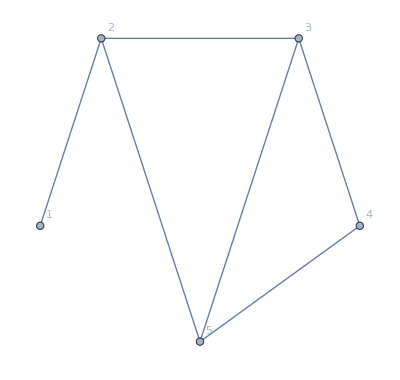

```mathematica
Parentheses2Polygon["(A1(A2(A3A4)))"]
```

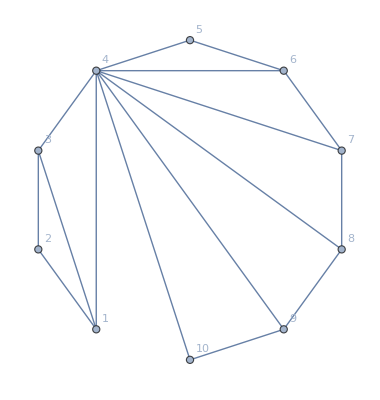

```mathematica
Parentheses2Polygon["(((A1A2)A3)(((((A4A5)A6)A7)A8)A9))"]
```

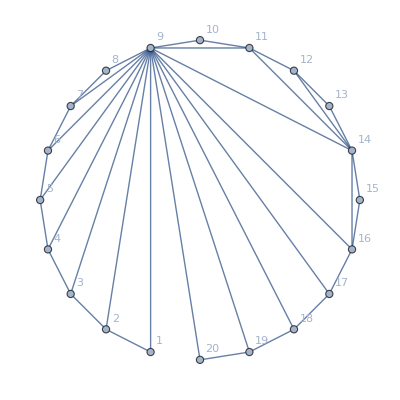

```mathematica
Parentheses2Polygon["((A1(A2(A3(A4(A5(A6(A7A8)))))))(((((((A9A10)(A11(A12A13)))(A14A15))A16)A17)A18)A19))"]
```

## I. DP for matrix chain multiplication

```mathematica
MCOP[p_]:= Module[{MAX = 10^15, n = Length[p]-1, ans, i,j,t, np},
M = ConstantArray[MAX, {n, n}];
S = ConstantArray[{}, {n,n}];
subproblem[i_, j_]:= Module[{k,q},
If[M[[i,j]] < MAX, Return[M[[i,j]]];];
If[i == j, M[[i,j]] = 0,
For[k = i, k ≤ j-1, k++,
q = subproblem[i, k] + subproblem[k+1, j] + p[[i]]*p[[k+1]]*p[[j+1]];
If[q < M[[i,j]], M[[i,j]] = q;];
];
];
Return[M[[i,j]]];
];
ans = subproblem[1, n];
For[i = 1, i≤ n-1, i++,
For[j = i+1, j ≤ n, j++,
For[t=i, t≤ j-1, t++,
If[M[[i,j]] == M[[i, t]] + M[[t+1, j]] + p[[i]]*p[[t+1]]*p[[j+1]],AppendTo[S[[i,j]], t]];
];
];
];

f[i_, x_, y_]:=x[[i]]<>#&/@y;
g[x_,y_] := Flatten[f[#,x,y]&/@Range[Length[x]]];

getoptimal[i_, j_]:=Module[{res,res1, temp, opt, k},
res = {""};
If[i == j, Return[{"A"<> ToString[j]} ], 
	res = # <>"("& /@ res;
	opt = S[[i,j]];
         res1 = {};
	For[k = 1, k≤ Length[opt], k++,
            temp  = g[res, getoptimal[i, opt[[k]]]];
            temp = g[temp, getoptimal[opt[[k]] + 1, j]];
	   temp = #<>")" &/@ temp;
	   res1 = Join[res1, temp];
       ];
Return[res1];
];
];
(*Print[M//TableForm];
Print[S//TableForm];*)
Print[ans];
np = getoptimal[1,n];
Print[np];
Parentheses2Polygon[#, p]&/@ np//TableForm
]


HorizontalArcs[p_]:= Module[{edges={},stack={}, p1,nodes,Vmin,v,t, i, len = Length[p]},
Vmin = Position[p, Min[p]][[1,1]];
p1 = Join[Drop[p,Vmin-1], Take[p, Vmin-1]];
nodes =Range[len];
i = 1;
v = p1[[i]];
While[i ≤ len-1,
	AppendTo[stack, i];
	v = p1[[++i]];
	While[p1[[Last[stack]]] > v,
		t = Last[stack];
		stack = Delete[stack, Length[stack]];
		AppendTo[edges, Last[stack]-> t];
		AppendTo[edges, t-> i];
	];
];

circleLayout[n_]:=Table[{Cos[-2π/n i-π/2],Sin[-2π/n i-π/2]},{i,n}];
Graph[nodes,DeleteDuplicates[edges],VertexLabels->Table[i ->p1[[i]], {i, len}], VertexCoordinates-> circleLayout[len]]
];
```

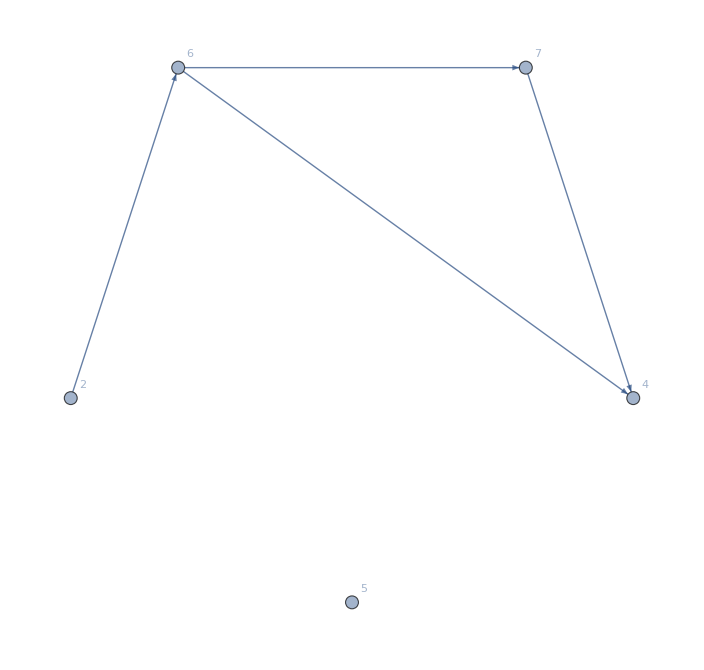

```mathematica
HorizontalArcs[{4,5,2,6,7}]
```

```mathematica
MCOP[{2,2,2,2,2}]
```

SetDelayed::write: Tag Graph in … is Protected.

24

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),A4)]]<>)],(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),A3)]]]<>),A4)]]<>)],(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),A4)]]<>)],(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),A3)]]<>)],(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),A3)]]]<>),A4)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

StringToStream::string: String expected at position 1 in ….

General::stop: Further output of StringToStream :: string will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

General::openx: $Failed is not open.

General::stop: Further output of General :: openx will be suppressed during this calculation.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

General::stop: Further output of ReadList :: nffil will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Select :: argb will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 2}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 2}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 2}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 2}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→2},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→2},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→2},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→2},VertexCoordinates→{{0,-1}}]

```mathematica
RandomInteger[{200, 1000},50]
```

{259,303,524,384,970,968,587,437,420,738,747,396,317,927,793,731,296,405,206,335,879,285,588,287,571,854,901,513,386,675,886,652,997,665,489,857,604,988,623,685,915,617,915,411,375,861,977,732,600,666}

```mathematica
MCOP[{216,399,302,355,209,299,356,376,352,395,326,203,316,329,311,216,336,254,232,318,270,282,370,228,381,278,270,328,204,389,386,203,212,239,360,315,253,247,211,227,294,217,259,318,346,395,266,347,316,306,312,365,230,267,298,317,226}]
```

SetDelayed::write: Tag Graph in … is Protected.

955184125

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),A4)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A6}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A7}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A8}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A9}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A10}]<>),A11)]]<>)]]<>)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A12}]<>),A13)]]]<>),A14)]]]<>),A15)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A16}]<>),A17)]]]<>),A18)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A19}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A20}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A21}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A22}]<>),A23)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A24}]<>),A25)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A26}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A27}]<>),A28)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A29}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A30}]<>),A31)]]<>)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A32}]<>),A33)]]]<>),A34)]]]<>),A35)]]]<>),A36)]]]<>),A37)]]]<>),A38)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A39}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A40}]<>),A41)]]<>)]]<>)]]]<>),A42)]]]<>),A43)]]]<>),A44)]]]<>),A45)]]]<>),A46)]]]<>),A47)]]]<>),A48)]]]<>),A49)]]]<>),A50)]]]<>),A51)]]]<>),A52)]]]<>),A53)]]]<>),A54)]]]<>),A55)]]]<>),A56)]]<>)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 216}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 216}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→216},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→216},VertexCoordinates→{{0,-1}}]

```mathematica
MCOP[{828,972,496,793,522,823,710,864,988,843,349,738,796,365,718,747,248,993,986,689,887,253,801,366,832,364,435,490,673,843,873,905,399,821,496,205,976,958,727,502,518,824,381,373,266,709,290,906,894,287}]
```

SetDelayed::write: Tag Graph in … is Protected.

4236012223

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A4}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A6}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A7}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A8}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A9}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A10}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A11}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A12}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A13}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A14}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A15}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A16}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A17}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A18}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A19}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A20}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A21}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A22}]<>),A23)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A24}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A25}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A26}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A27}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A28}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A29}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A30}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A31}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A32}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A33}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A34}]<>),A35)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A36}]<>),A37)]]]<>),A38)]]]<>),A39)]]]<>),A40)]]]<>),A41)]]]<>),A42)]]]<>),A43)]]]<>),A44)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A45}]<>),A46)]]<>)]]]<>),A47)]]]<>),A48)]]]<>),A49)]]<>)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 828}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 828}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→828},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→828},VertexCoordinates→{{0,-1}}]

```mathematica
a = RandomInteger[{200,205}, 10]
MCOP[a]
```

{201,205,201,205,200,205,200,205,202,205}

SetDelayed::write: Tag Graph in … is Protected.

65569215

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),A4)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),A6)]]<>)]]<>)],(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),A4)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),A6)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A7}]<>),A8)]]<>)]]]<>),A9)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 201}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 201}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→201},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→201},VertexCoordinates→{{0,-1}}]

```mathematica
a = RandomInteger[{100, 150}, 10]
MCOP[a]
```

{143,122,116,107,105,106,150,135,112,103}

SetDelayed::write: Tag Graph in … is Protected.

11808661

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A4}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A6}]<>),A7)]]]<>),A8)]]]<>),A9)]]<>)]]<>)]]<>)]]<>)]]<>)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 143}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 143}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→143},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→143},VertexCoordinates→{{0,-1}}]

```mathematica
MCOP[RandomInteger[{200,500}, 20]]
```

SetDelayed::write: Tag Graph in … is Protected.

444603628

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A4}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A5}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A6}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A7}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A8}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A9}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A10}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A11}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A12}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A13}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A14}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A15}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A16}]<>),A17)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A18}]<>),A19)]]<>)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 266}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 266}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→266},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→266},VertexCoordinates→{{0,-1}}]

```mathematica
MCOP[RandomInteger[{200,500}, 20]]
```

SetDelayed::write: Tag Graph in … is Protected.

341500589

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A2}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A3}]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A4}]<>),A5)]]<>)]]<>)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A6}]<>),A7)]]]<>),A8)]]]<>),A9)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A10}]<>),A11)]]<>)]]]<>),A12)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A13}]<>),A14)]]]<>),A15)]]]<>),A16)]]<>)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A17}]<>),A18)]]]<>),A19)]]<>)]]<>)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 335}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 335}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→335},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→335},VertexCoordinates→{{0,-1}}]

```mathematica
MCOP[{101,105,106,108,110,111,112,113}]
```

SetDelayed::write: Tag Graph in … is Protected.

7247356

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),A3)]]]<>),A4)]]]<>),A5)]]]<>),A6)]]]<>),A7)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 101}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 101}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→101},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→101},VertexCoordinates→{{0,-1}}]

```mathematica
a = RandomInteger[{204, 220}, 5]
MCOP[{200, 210, 212, 208, 209, 215, 208, 211, 203, 220, 208, 221}]
```

{211,206,204,204,219}

SetDelayed::write: Tag Graph in … is Protected.

88620480

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

StringJoin::string: String expected at position 1 in ….

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Join::heads: Heads List and … at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},Join[{},(-Graphics-)[(-Graphics-)[{(},{A1}]<>),A2)]]]<>),A3)]]]<>),A4)]]]<>),A5)]]]<>),A6)]]]<>),A7)]]]<>),A8)]]]<>),Join[{},(-Graphics-)[(-Graphics-)[{(},{A9}]<>),A10)]]<>)]]]<>),A11)]]

StringToStream::string: String expected at position 1 in StringToStream[{}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

First::nofirst: {} has zero length and no first element.

ToExpression::notstrbox: First[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

StringToStream::string: String expected at position 1 in ….

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::openx: $Failed is not open.

ReadList::nffil: File not found during ReadList[$Failed, Word, TokenWords → {"(", "A", ")"}].

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ≠ "A" &].

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First :: nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last :: nolast will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of {$Failed <-> 1 + $Failed}) beyond position 2 in Graph[{1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 200}, VertexCoordinates → {{0, -1}}, {1}, {$Failed <-> 1 + $Failed}, VertexLabels → {1 → 200}, VertexCoordinates → {{0, -1}}]. An option must be a rule or a list of rules.

Graph[{1},{$Failed<->1+$Failed},VertexLabels→{1→200},VertexCoordinates→{{0,-1}},{1},{$Failed<->1+$Failed},VertexLabels→{1→200},VertexCoordinates→{{0,-1}}]